### Parameters

```mathematica
ClearAll["Global`*"]
t=1;
mu=2;
d1=0.01;
d2=0.1;
g=0.05;
offset=Pi; (*Plots the interval [offset-pi, offset+pi]*)
nXY=150;nPhi=64; (*sampling*)
```

### Functions

```mathematica
Xi[x_,y_]:=-2 t (Cos[x]+Cos[y])-mu;

Delta[x_,y_,phi_]:=d1 (Cos[x]+Cos[y]) Exp[I*phi]+d2 (Sin[x]+I Sin[y])+0.05(Cos[x]+Cos[y])(*(Cos[x]-Cos[y])*);

Dispersion[x_,y_,phi_]:=Sqrt[Xi[x,y]^2+Abs[Delta[x,y,phi]]^2];

vSquared[x_,y_,phi_]:=(1-Xi[x,y]/Dispersion[x,y,phi])/2;

Intensity[x_,y_,phi_]:=(vSquared[x,y,phi]/Pi)*(g/((-Dispersion[0,0,phi]+Dispersion[x,y,phi])^2+g^2));
phiValues=Subdivide[0,2 Pi-2 Pi/nPhi,nPhi-1];
expFactors=Exp[-I*phiValues];

c1Data=ParallelTable[Module[{intensities},
intensities=Table[Intensity[x,y,p],{p,phiValues}];
Mean[intensities*expFactors]],{y,Reverse[Subdivide[offset-Pi,offset+Pi,nXY-1]]},{x,Subdivide[offset-Pi,offset+Pi,nXY-1]}];
```

### Plotting

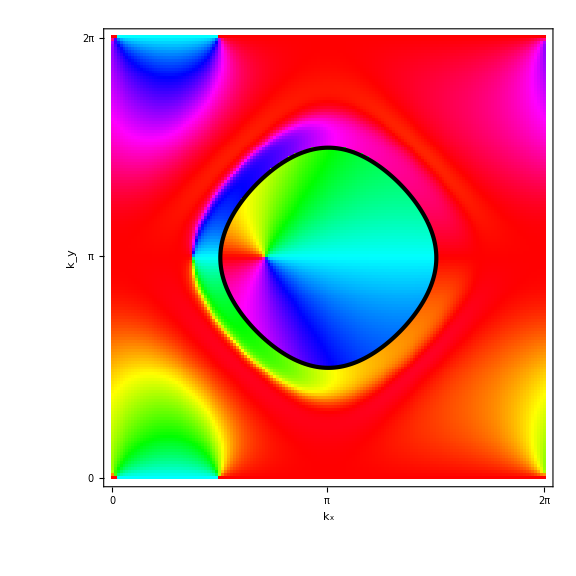

```mathematica
tickPosY={{1,Style["2π",24]},{nXY/2,Style["π",24]},{nXY,Style["0",24]}};
tickPosX={{1,Style["0",24]},{nXY/2,Style["π",24]},{nXY,Style["2π",24]}};

(*Fourier phase data*)
phasePlot=ArrayPlot[Arg[c1Data],DataRange->{{1,nXY},{1,nXY}},ColorFunction->Hue,PlotRange->{-Pi,Pi},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameTicks->{{({nXY+1-#[[1]],#[[2]]}&/@tickPosY),None},{tickPosX,None}},FrameLabel->{Style[Subscript["k","y"],28,FontFamily->"Times New Roman",Black],Style[Subscript["k","x"],28,FontFamily->"Times New Roman",Black]},LabelStyle->Directive[Black,52,FontFamily->"Times New Roman"],ImageSize->Large];

(*Fermi surface contour*)
kFromIndex[i_]:=offset-Pi+(i-1) 2 Pi/(nXY-1);

fermiSurface=ContourPlot[Xi[kFromIndex[x],kFromIndex[y]],{x,1,nXY},{y,1,nXY},Contours->{0},ContourShading->None,ContourStyle->Directive[Black,AbsoluteThickness[3]],PlotPoints->100,MaxRecursion->2,Frame->False,Axes->False];


legendTicks={{-Pi,Style["-π",24]},{-Pi/2,Style["-π/2",24]},{0,Style["0",24]},{Pi/2,Style["π/2",24]},{Pi,Style["π",24]}};


phaseLegend=Column[{Style["Phase",28,FontFamily->"Times New Roman",Black],Graphics[Table[{Hue[(j-0.5)/256],EdgeForm[],Rectangle[{0,-Pi+2 Pi (j-1)/256},{1,-Pi+2 Pi j/256}]},{j,1,256}],Frame->{{False,True},{False,False}},FrameTicks->{{None,legendTicks},{None,None}},FrameTicksStyle->Directive[Black,24,FontFamily->"Times New Roman"],PlotRange->{{0,1},{-Pi,Pi}},PlotRangePadding->None,ImageSize->{115,320},ImagePadding->{{3,77},{8,8}}]},Alignment->Center];


Print[Legended[Show[phasePlot,fermiSurface,PlotRange->{{1,nXY},{1,nXY}},RotateLabel->False],Placed[phaseLegend,Right]]];
```